# Error Calculation

#### Calculate Hesse Matrix

```mathematica
Hesse = {{H11,H12,H13,H14,H15,H16},{H12,H22,H23,H24,H25,H26},{H13,H23,H33,H34,H35,H36},{H14,H24,H34,H44,H45,H46},{H15,H25,H35,H45,H55,H56},{H16,H26,H36,H46,H56,H66}};
```

```mathematica
Params = {Tgχ,TG0,Tmχ,TMG,Th,TgAV};
```

Warning: Calculation of Hesse Matrix takes about 20-30 Minutes!

```mathematica
For[i=1,i<7,i++,
For[j=1,j<7,j++,If[i>j,Hesse[[i,j]]=Hesse[[j,i]],Hesse[[i,j]]=D[G,Params[[i]],Params[[j]]]/.{Tgχ->Pgχ,TG0->PG0,Tmχ->Pmχ,TMG->PMG,Th->Ph,TgAV->PgAV}//ComplexExpand]]]
```

```mathematica
MatrixForm[Hesse]
```

(0.00207115+0. ⅈ | 0.00107034+0. ⅈ | -0.00106253+0. ⅈ | -0.00220654+0. ⅈ | 0.0577483+0. ⅈ | 0.0000291527+0. ⅈ
0.00107034+0. ⅈ | 0.000604752+0. ⅈ | -0.000587299+0. ⅈ | -0.00134618+0. ⅈ | 0.0356743+0. ⅈ | 0.0000150498+0. ⅈ
-0.00106253+0. ⅈ | -0.000587299+0. ⅈ | 0.00243336+0. ⅈ | 0.00128186+0. ⅈ | -0.0370082+0. ⅈ | -5.66201×10^-7+0. ⅈ
-0.00220654+0. ⅈ | -0.00134618+0. ⅈ | 0.00128186+0. ⅈ | 0.00334892+0. ⅈ | -0.0816172+0. ⅈ | -0.0000310677+0. ⅈ
0.0577483+0. ⅈ | 0.0356743+0. ⅈ | -0.0370082+0. ⅈ | -0.0816172+0. ⅈ | 2.53646 | 0.000813971
0.0000291527+0. ⅈ | 0.0000150498+0. ⅈ | -5.66201×10^-7+0. ⅈ | -0.0000310677+0. ⅈ | 0.000813971 | 1.70149×10^-6)

Check Eigenvalues, they should be positive

```mathematica
Eigenvalues[Hesse]
```

{2.54144,0.00196591,0.00111503,0.000388748,3.35216×10^-6,1.17473×10^-6}

#### Previously calculated Hesse matrices

```mathematica
{Pgχ,Pλ1,Pmχ,PMG,PG0,Ph,PgAV}
```

{838.394,0,569.546,1662.69,642.533,-14.6953,90.421}

Relevant for Paper:

```mathematica
{Pgχ,Pλ1,Pmχ,PMG,PG0,Ph,PgAV}={155.62493338022705,0,538.67847879117,1672.3162409598303,668.9285058639134,-10.112774884439935,10946.613366851072};
```

```mathematica
HesseNewDecayWidth=({{0.002071145883716891+0. ⅈ, 0.001070344193234832+0. ⅈ, -0.0010625327771970703+0. ⅈ, -0.0022065442087638473+0. ⅈ, 0.05774828846569997+0. ⅈ, 0.000029152681792962763+0. ⅈ}, {0.001070344193234832+0. ⅈ, 0.0006047517241851967+0. ⅈ, -0.0005872985200656838+0. ⅈ, -0.0013461835303470503+0. ⅈ, 0.03567432777347437+0. ⅈ, 0.000015049761083993633+0. ⅈ}, {-0.0010625327771970703+0. ⅈ, -0.0005872985200656838+0. ⅈ, 0.0024333592182867294+0. ⅈ, 0.0012818564850071844+0. ⅈ, -0.03700822696948881+0. ⅈ, -5.662010719090018*^-7+0. ⅈ}, {-0.0022065442087638473+0. ⅈ, -0.0013461835303470503+0. ⅈ, 0.0012818564850071844+0. ⅈ, 0.0033489216903421315+0. ⅈ, -0.08161718090889195+0. ⅈ, -0.00003106767504463501+0. ⅈ}, {0.05774828846569997+0. ⅈ, 0.03567432777347437+0. ⅈ, -0.03700822696948881+0. ⅈ, -0.08161718090889195+0. ⅈ, 2.5364586109674083, 0.000813971205919562}, {0.000029152681792962763+0. ⅈ, 0.000015049761083993633+0. ⅈ, -5.662010719090018*^-7+0. ⅈ, -0.00003106767504463501+0. ⅈ, 0.000813971205919562, 1.7014863313739233*^-6}});
```

#### Error calculation

```mathematica
Hesse = 1/2HesseNewDecayWidth;
```

```mathematica
InverseH=Inverse[Hesse];
SqrInverseH=Sqrt[InverseH];
```

```mathematica
{dPgχ,dPG0,dPmχ,dPMG,dPh,dPgAV}={Part[SqrInverseH,1,1],Part[SqrInverseH,2,2],Part[SqrInverseH,3,3],Part[SqrInverseH,4,4],Part[SqrInverseH,5,5],Part[SqrInverseH,6,6]}
```

{214.941+0. ⅈ,738.25+0. ⅈ,34.7608+0. ⅈ,120.044+0. ⅈ,3.12013+0. ⅈ,1303.94+0. ⅈ}

#### Plots

```mathematica
DiscretePlot3D[F/.{Tmχ->Pmχ,TMG->PMG,TG0->PG0,Th->Ph,TgAV->PgAV},{Tgχ,Pgχ-15,Pgχ+15,1},{Tλ1,Pλ1-5, Pλ1+5,1}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[F/.{Tmχ->Pmχ,Tλ1 -> Pλ1,TMG->PMG,Th->Ph,TgAV->PgAV},{Tgχ,Pgχ-15,Pgχ+15,1},{TG0,PG0-50, PG0+50,10}]
```

-Graphics3D-

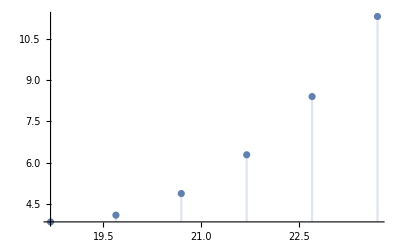

```mathematica
DiscretePlot[F/.{Tλ1->Pλ1,Tmχ->Pmχ,TMG->PMG,TG0->PG0,Th->Ph,TgAV->PgAV},{Tgχ,Pgχ,Pgχ+5,1}]
```

#### Continue Error Calculation

```mathematica
{λlin,bb}=Eigensystem[Hesse];
λ=bb.Hesse.Transpose[bb];
```

Check:

```mathematica
dgχ = Sqrt[Sum[bb[[l,1]]^2/λlin[[l]],{l,1,6}]]
```

214.941+0. ⅈ

```mathematica
list = {l1,l2,l3,l4,l5,l6};
```

```mathematica
dpa[f_]:=For[i=1,i<7,i++,list[[i]]=D[f[Tgχ,TG0,Tmχ,TMG,Th,TgAV],Params[[i]]]/.{Tgχ->Pgχ,Tmχ->Pmχ,TMG->PMG,TG0->PG0,Th->Ph,TgAV->PgAV}//FunctionExpand]
```

```mathematica
Dpa[f_]:= For[i=1,i<2,i++,dpa[f];Return[{list,list, list,list,list,list}]]
```

```mathematica
Dpa[FmH];
```

```mathematica
KK[f_]:=Dpa[f].Transpose[bb].Sqrt[Inverse[λ]]
α[f_]:=Abs[{KK[f][[1,1]],KK[f][[2,2]],KK[f][[3,3]],KK[f][[4,4]],KK[f][[5,5]],KK[f][[6,6]]}]
Da[f_] :=Sqrt[α[f].α[f]]
```

Run ExpressionsToFunctionsWithGlueball First!

```mathematica
Da[FmH]
```

34.4275

```mathematica
Da[FmS]
```

133.705

```mathematica
Da[FmG]
```

50.0233

```mathematica
Da[ΓH]
```

148.118

```mathematica
Da[ΓS]
```

39.0536

```mathematica
Da[ΓG]
```

6.4987

```mathematica
Da[A00]
```

0.0164216

```mathematica
Da[A02]
```

0.00504606

```mathematica
χ0[Tgχ_,TG0_,Tmχ_,TMG_,Th_,TgAV_] :=χ0[Tgχ,TG0,0,Tmχ,TMG,Th,TgAV]
Mσ[Tgχ_,TG0_,Tmχ_,TMG_,Th_,TgAV_] :=Mσ[Tgχ,TG0,0,Tmχ,TMG,Th,TgAV]
c[Tgχ_,TG0_,Tmχ_,TMG_,Th_,TgAV_] :=c[Tgχ,TG0,0,Tmχ,TMG,Th,TgAV]
μ[Tgχ_,TG0_,Tmχ_,TMG_,Th_,TgAV_]  :=μ[Tgχ,TG0,0,Tmχ,TMG,Th,TgAV]
m1[Tgχ_,TG0_,Tmχ_,TMG_,Th_,TgAV_]  :=m1[Tgχ,TG0,0,Tmχ,TMG,Th,TgAV]
```

```mathematica
Da[χ0]
Da[Mσ]
Da[c]
Da[μ]
Da[m1]
```

17.4514

0.

10909.5

0.

316.626